# Shape - preserving functions

## Introduction

This Mathematica notebook is licensed under a  
It creates the demonstrations used in my post Maps. Graphs created using this notebook may be found at http://www.abstractmath.org/MM/Mathematica/Shape/

I hope anyone interested will feel free to improve this work and to use it in their own publications and coursework.

## Preliminaries

Colors

```mathematica
c1=RGBColor[.3,.6,.3];c2=RGBColor[.7,.2,.1];c3=RGBColor[.5,.3,.5]
```

-Graphics-

Sample matrix to work with

```mathematica
mat:={{-.6,1.3},{-1,.5}}
```

```mathematica
TableForm[{{-0.6,1.3},{-1,0.5}}]
```

-0.6 | 1.3
-1 | 0.5

```mathematica
mat//Det
```

1.

```mathematica
imat=mat//Inverse
```

{{0.5,-1.3},{1.,-0.6}}

Circle

```mathematica
cc[c_,r_,col_]:=ParametricPlot[{ r Cos[t],r  Sin[t]}+c,{t,0,2Pi},PlotStyle->{Thick,col},ImageSize->100]
```

```mathematica
cc[{1,1},.6,Red]
```

-Graphics-

Straight line

```mathematica
ln[p_,q_,color_]:=ParametricPlot[p x + q(1-x),{x,0,1},PlotStyle->{Thick,color},ImageSize->200]
```

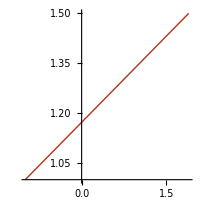

```mathematica
ln[{1.9,1.5},{-1,1},c2]
```

Rectangle

```mathematica
rect[p_,q_,color_]:=Show[
{
ln[p,{p[[1]],q[[2]]},color],ln[{p[[1]],q[[2]]},q,color],ln[q,{q[[1]],p[[2]]},color],ln[{q[[1]],p[[2]]},p,color]
}
]
```

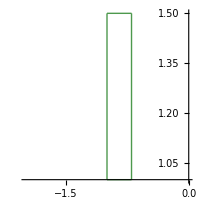

```mathematica
rect[{-1,1},{-.7,1.5},c1]
```

Special triangle

```mathematica
tr[p_,color_]:={ln[p,{p[[1]]-.2,p[[2]]+.8},color],ln[{p[[1]]-.2,p[[2]]+.8},{p[[1]]+.2,p[[2]]+.8},color],ln[{p[[1]]+.2,p[[2]]+.8},p,color]}
```

```mathematica
Show[tr[{1,1},c3],ImageSize->100,PlotRange->{{0.5,1.3},{.5,2}},AspectRatio->Automatic]
```

-Graphics-

Display shapes

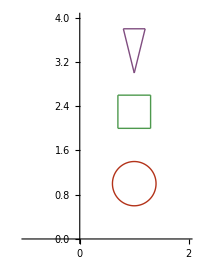

```mathematica
Show[
{cc[{1,1},.4,c2],
rect[{1.3,2},{.7,2.6},c1],
tr[{1,3},c3]
},Axes->True,AxesOrigin->{0,0},PlotRange->{{-1,2},{0,4}},ImageSize->200
]
```

Image of circle

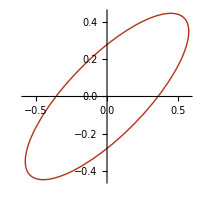

```mathematica
ParametricPlot[mat.#&[{ .4 Cos[t],.4  Sin[t]}+0],{t,0,2Pi},PlotStyle->{Thick,c2},ImageSize->200]
```

```mathematica
apcc[c_,r_,col_,ap_]:=ParametricPlot[ap[{ r Cos[t],r  Sin[t]}+c],{t,0,2Pi},PlotStyle->{Thick,col},ImageSize->200]
```

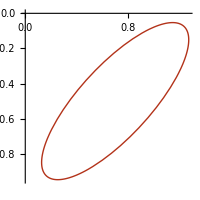

```mathematica
apcc[{1,1},.4,c2,mat.#&]
```

```mathematica
apcc[{0,0},.4,c2,mat.#&]
```

-Graphics-

Image of rectangle

```mathematica
ln[p_,q_,color_]:=ParametricPlot[p x + q(1-x),{x,0,1},PlotStyle->{Thick,color},ImageSize->100]
```

```mathematica
apln[p_,q_,color_,ap_]:=ParametricPlot[ap[p x + q(1-x)],{x,0,1},PlotStyle->{Thick,color},ImageSize->100]
```

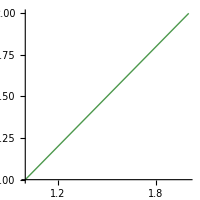

```mathematica
ln[{1,1},{2,2},c1]
```

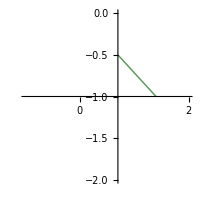

```mathematica
Show[apln[{1,1},{2,2},c1,mat.#&],PlotRange->{{-1,2},{-2,0}},AspectRatio->Automatic,ImageSize->200]
```

```mathematica
aprect[p_,q_,color_,ap_]:=Show[
{
apln[p,{p[[1]],q[[2]]},color,ap],apln[{p[[1]],q[[2]]},q,color,ap],apln[q,{q[[1]],p[[2]]},color,ap],apln[{q[[1]],p[[2]]},p,color,ap]
}
]
```

```mathematica
rect[{-1,1},{-.7,1.5},c1]
```

-Graphics-

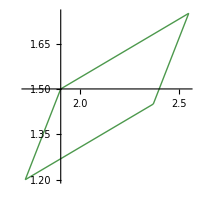

```mathematica
Show[aprect[{-1,1},{-.7,1.5},c1,mat.#&],PlotRange->Automatic,AspectRatio->Automatic,ImageSize->200]
```

Image of triangle

```mathematica
tr[p_,color_]:={ln[p,{p[[1]]-.2,p[[2]]+.8},color],ln[{p[[1]]-.2,p[[2]]+.8},{p[[1]]+.2,p[[2]]+.8},color],ln[{p[[1]]+.2,p[[2]]+.8},p,color]}
```

```mathematica
aptr[p_,color_,ap_]:={apln[p,{p[[1]]-.2,p[[2]]+.8},color,ap],apln[{p[[1]]-.2,p[[2]]+.8},{p[[1]]+.2,p[[2]]+.8},color,ap],apln[{p[[1]]+.2,p[[2]]+.8},p,color,ap]}
```

```mathematica
Show[aptr[{1,1},c3,mat.#&]]
```

-Graphics-

Variable matrix with det 1

```mathematica
df[a_,b_,c_,d_]:=-b c+a d
```

```mathematica
Solve[-b c+a d==1,{a}]
```

{{a→(1+b c)/d}}

```mathematica
Solve[-b c+a==1,{a}]
```

{{a→1+b c}}

## Display area-preserving functions

```mathematica
Manipulate[
Module[
{mat},
mat[b_,c_,d_]:={{(1+b c)/d,b},{c,d}};
Show[Graphics[Text[mat[b,c,d]//MatrixForm,{7,4}]],
cc[{1,1},.4,c2],
apcc[{1,1},.4,c2,mat[b,c,d].#&],
rect[{1.3,2},{.7,2.6},c1],
aprect[{1.3,2},{.7,2.6},c1,mat[b,c,d].#&],
tr[{1,3},c3],aptr[{1,3},c3,mat[b,c,d].#&],
Axes->True,AxesOrigin->{0,0},PlotRange->{{-4,9},{-1,6}},AspectRatio->7/13,ImageSize->400
]],
{{b,.7},-1,1,Appearance->"Open"},{{c,.4},-1,1,Appearance->"Open"},{{d,1},0.5,1.25,Appearance->"Open"},SaveDefinitions->True
]
```

Examples

```mathematica
apf[b_,c_,d_]:=Module[
{mat},
mat[b,c,d]={{(1+b c)/d,b},{c,d}};
Show[Graphics[Text[mat[b,c,d]//MatrixForm,{7,4}]],
cc[{1,1},.4,c2],
apcc[{1,1},.4,c2,mat[b,c,d].#&],
rect[{1.3,2},{.7,2.6},c1],
aprect[{1.3,2},{.7,2.6},c1,mat[b,c,d].#&],
tr[{1,3},c3],aptr[{1,3},c3,mat[b,c,d].#&],
Axes->True,AxesOrigin->{0,0},PlotRange->{{-4,9},{-1,6}},AspectRatio->7/13,ImageSize->400
]]
```

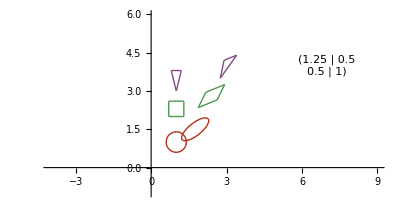

```mathematica
apf[.5,.5,1]
```

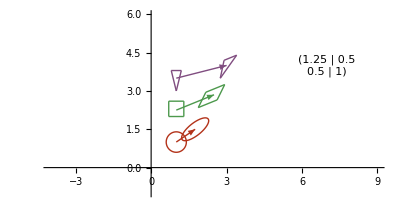

```mathematica
Show[apf[.5,.5,1],Graphics[{Arrowheads[0.02],c3,Arrow[{{1,3.5},{3,4}},0],c1,Arrow[{{1,2.25},{2.5,2.85}},0],c2,Arrow[{{1,1},{1.75,1.5}},0]}]]
```

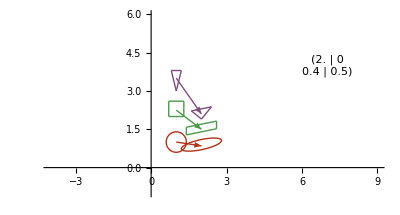

```mathematica
Show[apf[0,.4,.5],Graphics[{Arrowheads[0.02],c3,Arrow[{{1,3.5},{2,2.1}},0],c1,Arrow[{{1,2.25},{2,1.5}},0],c2,Arrow[{{1,1},{2,0.85}},0]}]]
```

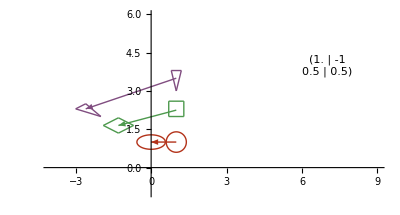

```mathematica
Show[apf[-1,.5,.5],Graphics[{Arrowheads[0.02],c3,Arrow[{{1,3.5},{-2.6,2.3}},0],c1,Arrow[{{1,2.25},{-1.3,1.65}},0],c2,Arrow[{{1,1},{0,1}},0]}]]
```

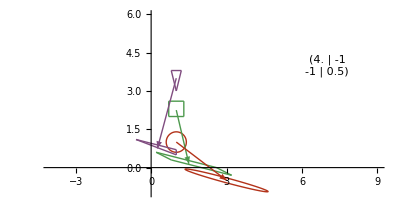

```mathematica
Show[apf[-1,-1,.5],Graphics[{Arrowheads[0.02],c3,Arrow[{{1,3.5},{.25,.75}},0],c1,Arrow[{{1,2.25},{1.5,.15}},0],c2,Arrow[{{1,1},{3,-.5}},0]}]]
```

## Angle-preserving functions

```mathematica
expmat={{Cos[t],-Sin[t]},{Sin[t],Cos[t]}}
```

{{Cos[t],-Sin[t]},{Sin[t],Cos[t]}}

```mathematica
expmat//MatrixForm
```

(Cos[t] | -Sin[t]
Sin[t] | Cos[t])

```mathematica
rnd[x_]:=Round[x,.01]
```

```mathematica
Manipulate[
Module[
{mat},
mat[a_,t_]:=a{{Cos[t],-Sin[t]},{Sin[t],Cos[t]}};
Show[Graphics[Text[rnd[mat[a,t]]//MatrixForm,{5,4}]],
cc[{1,1},.4,c2],
apcc[{1,1},.4,c2,mat[a,t].#&],
rect[{1.3,2},{.7,2.6},c1],
aprect[{1.3,2},{.7,2.6},c1,mat[a,t].#&],
tr[{1,3},c3],aptr[{1,3},c3,mat[a,t].#&],
Axes->True,AxesOrigin->{0,0},PlotRange->{{-8,8},{-3,8}},AspectRatio->11/17,ImageSize->400
]],
{{t,.7},-Pi/2,Pi/2,-.1,Appearance->"Open"},{{a,1},0,2,Appearance->"Open"}
]
```

```mathematica
epf[t_,a_]:=Module[
{mat},
mat[a,t]=a{{Cos[t],-Sin[t]},{Sin[t],Cos[t]}};
Show[Graphics[Text[rnd[mat[a,t]]//MatrixForm,{5,4}]],
cc[{1,1},.4,c2],
apcc[{1,1},.4,c2,mat[a,t].#&],
rect[{1.3,2},{.7,2.6},c1],
aprect[{1.3,2},{.7,2.6},c1,mat[a,t].#&],
tr[{1,3},c3],aptr[{1,3},c3,mat[a,t].#&],
Axes->True,AxesOrigin->{0,0},PlotRange->{{-8,8},{-3,8}},AspectRatio->11/17,ImageSize->400
]]
```

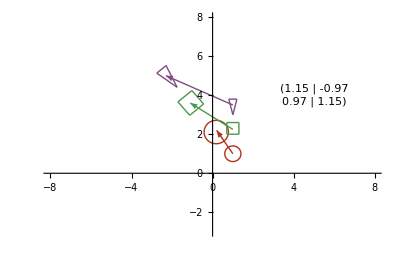

```mathematica
Show[epf[.7,1.5],Graphics[{Arrowheads[0.02],c3,Arrow[{{1,3.5},{-2.3,5}},0],c1,Arrow[{{1,2.25},{-1.1,3.6}},0],c2,Arrow[{{1,1},{.2,2.2}},0]}]]
```

```mathematica
{{1.15,-0.97},{0.97,1.15}}
```

{{1.15,-0.97},{0.97,1.15}}

```mathematica
Pi/2//N
```

1.5708

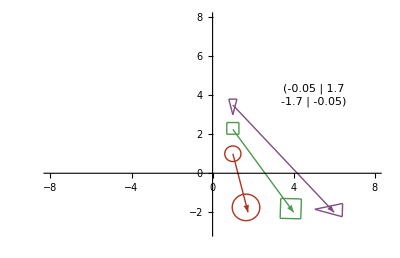

```mathematica
Show[epf[-1.6,1.7],Graphics[{Arrowheads[0.02],c3,Arrow[{{1,3.5},{6,-2}},0],c1,Arrow[{{1,2.25},{4,-2}},0],c2,Arrow[{{1,1},{1.75,-2}},0]}]]
```

```mathematica
{{-.05,1.7},{-1.7,-.05}}
```

{{-0.05,1.7},{-1.7,-0.05}}

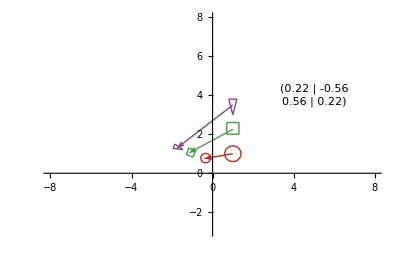

```mathematica
Show[epf[1.2,.6],Graphics[{Arrowheads[0.02],c3,Arrow[{{1,3.5},{-1.75,1.3}},0],c1,Arrow[{{1,2.25},{-1.15,1.05}},0],c2,Arrow[{{1,1},{-.4,.75}},0]}]]
```

```mathematica
{{.22,-.56},{.56,.22}}
```

{{0.22,-0.56},{0.56,0.22}}

Some endographs

```mathematica
matr:={{2,0},{.4,.5}}
```

```mathematica
matr.{x,y}
```

{2 x,0.4 x+0.5 y}

```mathematica
bigrg:={{-10,10},{-5,10}}
```

```mathematica
latt:=Flatten[Table[{i,j},{i,-15,15,1},{j,-8,15,1}],1]
```

```mathematica
littlelatt:=Flatten[Table[{i,j},{i,-1,2,.5},{j,-2,1,.5}],1]
```

```mathematica
littlelatt
```

{{-1.,-2.},{-1.,-1.5},{-1.,-1.},{-1.,-0.5},{-1.,0.},{-1.,0.5},{-1.,1.},{-0.5,-2.},{-0.5,-1.5},{-0.5,-1.},{-0.5,-0.5},{-0.5,0.},{-0.5,0.5},{-0.5,1.},{0.,-2.},{0.,-1.5},{0.,-1.},{0.,-0.5},{0.,0.},{0.,0.5},{0.,1.},{0.5,-2.},{0.5,-1.5},{0.5,-1.},{0.5,-0.5},{0.5,0.},{0.5,0.5},{0.5,1.},{1.,-2.},{1.,-1.5},{1.,-1.},{1.,-0.5},{1.,0.},{1.,0.5},{1.,1.},{1.5,-2.},{1.5,-1.5},{1.5,-1.},{1.5,-0.5},{1.5,0.},{1.5,0.5},{1.5,1.},{2.,-2.},{2.,-1.5},{2.,-1.},{2.,-0.5},{2.,0.},{2.,0.5},{2.,1.}}

```mathematica
Point[#]&/@littlelatt;
```

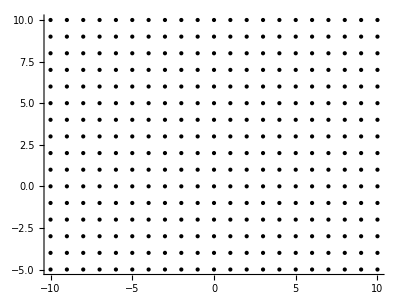

```mathematica
Show[
Graphics[
Point[#]&/@latt
],PlotRange->bigrg,Axes->True]
```

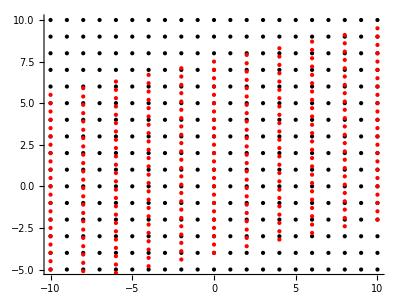

```mathematica
Show[
Graphics[
{Point[#]&/@latt,Red,Point[matr.#]&/@latt
}],PlotRange->bigrg,Axes->True]
```

```mathematica
plotboth[matrix_,arr_,rg_]:=Show[
Graphics[
{Point[#]&/@arr,Red,Point[matrix.#]&/@arr
}],PlotRange->rg,Axes->True]
```

```mathematica
plotboth[matr,latt,bigrg]
```

-Graphics-

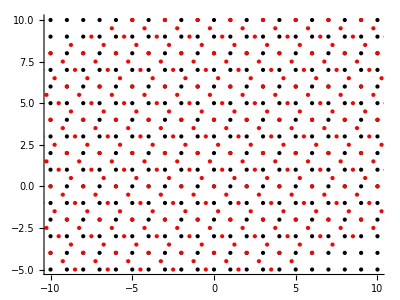

```mathematica
plotboth[{{1.25,.5},{.5,1}},latt,bigrg]
```

```mathematica
plotbotharrs[matrix_,arr_,rg_,arrowheadsize_]:=Show[
Graphics[
{Arrowheads[arrowheadsize],Point[#]&/@arr,Red,Point[matrix.#]&/@arr,Arrow[{#,matrix.#},0]&/@arr
}],PlotRange->rg,Axes->True]
```

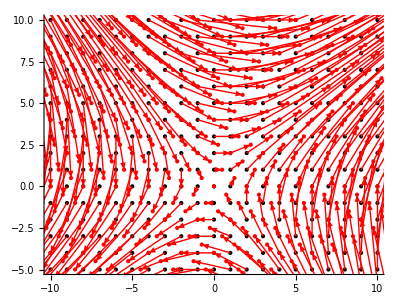

```mathematica
plotbotharrs[{{1.25,.5},{.5,1}},latt,bigrg,.02]
```

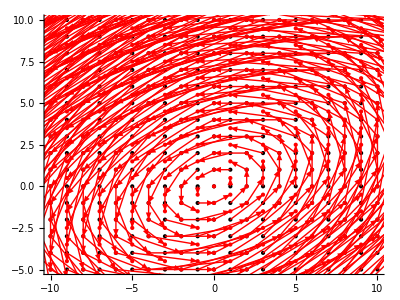

```mathematica
plotbotharrs[{{1,-1},{.5,.5}},latt,bigrg,.02]
```

```mathematica
{{1.15,-0.97},{0.97,1.15}}
```

{{1.15,-0.97},{0.97,1.15}}

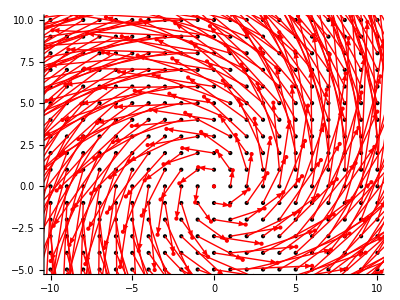

```mathematica
plotbotharrs[{{1.15,-0.97},{0.97,1.15}},latt,bigrg,.02]
```

```mathematica
{{.22,-.56},{.56,.22}}
```

{{0.22,-0.56},{0.56,0.22}}

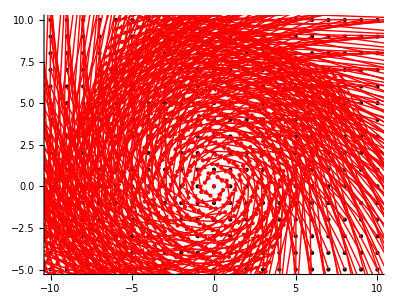

```mathematica
plotbotharrs[{{.22,-.56},{.56,.22}},latt,bigrg,.02]
```

```mathematica
{{-.05,1.7},{-1.7,-.05}}
```

{{-0.05,1.7},{-1.7,-0.05}}

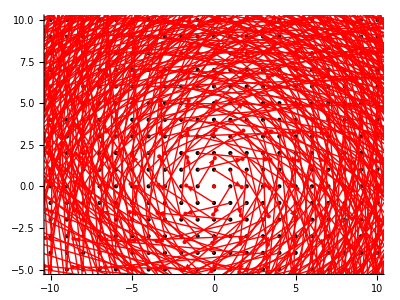

```mathematica
plotbotharrs[{{-.05,1.7},{-1.7,-.05}},latt,bigrg,.02]
```